```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_],LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_,b_]=c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_,b_],TraditionalForm] is Protected.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/vfigueira/Documentos/vvfigueira.github.io/WolframLinux/Teste1/DF2"]
```

Successfully patched FeynArts.

```mathematica
diags=InsertFields[CreateTopologies[0,1->2],{V[1]}->{V[1],V[1]},InsertionLevel->{Classes},Model->"/home/vfigueira/Documentos/vvfigueira.github.io/WolframLinux/Teste1/DF2/DF2", GenericModel ->"/home/vfigueira/Documentos/vvfigueira.github.io/WolframLinux/Teste1/DF2/DF2"];
```

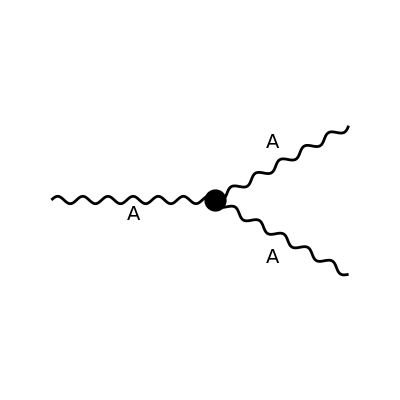

```mathematica
Paint[diags,ColumnsXRows->{3,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags, PreFactor->1],IncomingMomenta->{-p1},OutgoingMomenta->{p2,p3},LoopMomenta->{},ChangeDimension->4,List->False]
```

Pair[LorentzIndex[Lor1],Momentum[Polarization[-p1,ⅈ]]] Pair[LorentzIndex[Lor2],Momentum[Polarization[p2,-ⅈ]]] Pair[LorentzIndex[Lor3],Momentum[Polarization[p3,-ⅈ]]] SumOver[SUNIndex[Glu1],3,External] SumOver[SUNIndex[Glu2],3,External] SumOver[SUNIndex[Glu3],3,External] (-g m^2 Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g m^2 Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g m^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g m^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g m^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g m^2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[LorentzIndex[Lor3],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[LorentzIndex[Lor3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[LorentzIndex[Lor3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[LorentzIndex[Lor3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[LorentzIndex[Lor3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[LorentzIndex[Lor3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p1],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p1],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[Momentum[p1],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[Momentum[p1],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p2]] Pair[Momentum[p1],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p3]] Pair[Momentum[p1],Momentum[p1]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p1],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p1],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[Momentum[p1],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[Momentum[p1],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p1],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p1],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p2]] Pair[Momentum[p1],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p3]] Pair[Momentum[p1],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p2],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 g Pair[LorentzIndex[Lor1],Momentum[p3]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p2],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[Momentum[p2],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p3]] Pair[Momentum[p2],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p1]] Pair[Momentum[p2],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p3]] Pair[Momentum[p2],Momentum[p2]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[Momentum[p2],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[Momentum[p2],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p1]] Pair[Momentum[p2],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p3]] Pair[Momentum[p2],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],Momentum[p1]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+2 g Pair[LorentzIndex[Lor1],Momentum[p2]] Pair[LorentzIndex[Lor2],LorentzIndex[Lor3]] Pair[Momentum[p3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-2 g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p1]] Pair[Momentum[p3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor3]] Pair[LorentzIndex[Lor2],Momentum[p2]] Pair[Momentum[p3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]+g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p1]] Pair[Momentum[p3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]]-g Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]] Pair[LorentzIndex[Lor3],Momentum[p2]] Pair[Momentum[p3],Momentum[p3]] SUNF[SUNIndex[Glu1],SUNIndex[Glu2],SUNIndex[Glu3]])

```mathematica
FCClearScalarProducts[];
SetMandelstam[x,{ p1 , p2, p3} ,{ 0 , 0 , 0} ];
```

```mathematica
amp[1]=amp[0] // Contract // SUNSimplify
```

(-g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]]-2 g Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]]+2 g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]]+2 g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]]-2 g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]]+g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]+2 g Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-2 g Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-g m^2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+2 g Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[p2]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g m^2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 g Pair[Momentum[p1],Momentum[p1]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[p3]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-g Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[p3]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-g Pair[Momentum[p1],Momentum[p1]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]-g Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g Pair[Momentum[p2],Momentum[p2]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g m^2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[p2]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[p1]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p2],Momentum[p3]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 g Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[p3]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[p3]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g m^2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 g Pair[Momentum[p1],Momentum[p1]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p2],Momentum[p2]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[p2]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g m^2 Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[p1]] Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[p3]] Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[p3]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+2 g Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[p3]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g m^2 Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p1],Momentum[p1]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[p2]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-2 g Pair[Momentum[p2],Momentum[p2]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]) SumOver[SUNIndex[FCGV[sun531]],3,External] SumOver[SUNIndex[FCGV[sun532]],3,External] SumOver[SUNIndex[FCGV[sun533]],3,External] SUNF[SUNIndex[FCGV[sun531]],SUNIndex[FCGV[sun532]],SUNIndex[FCGV[sun533]]]

```mathematica
amp[2] = amp[1] // ExpandScalarProduct
```

```mathematica
amp[3] =FeynAmpDenominatorExplicit[amp[2]]
```

SumOver[SUNIndex[FCGV[sun341]],3,External] SumOver[SUNIndex[FCGV[sun342]],3,External] SumOver[SUNIndex[FCGV[sun343]],3,External] SUNF[SUNIndex[FCGV[sun341]],SUNIndex[FCGV[sun342]],SUNIndex[FCGV[sun343]]] (-g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]]-2 g Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]]+2 g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]]+2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]]+2 g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]]-2 g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]]-2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]]+g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]+2 g Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]+g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-2 g Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]]-g m^2 Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g m^2 Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]]+g m^2 Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g m^2 Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]]-g m^2 Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+g m^2 Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]]+1/2 g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[1,2]+Pair[Momentum[p3],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[1,2]-1/2 g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[1,2]-Pair[Momentum[p3],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[1,2]-Pair[Momentum[p2],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]] x[1,3]-1/2 g Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]] x[1,3]+1/2 g Pair[Momentum[p1],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[1,3]+Pair[Momentum[p2],Momentum[Polarization[-p1,ⅈ]]] Pair[Momentum[Polarization[p2,-ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[1,3]+Pair[Momentum[p1],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]] x[2,3]+1/2 g Pair[Momentum[p3],Momentum[Polarization[p3,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p2,-ⅈ]]] x[2,3]-Pair[Momentum[p1],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[2,3]-1/2 g Pair[Momentum[p2],Momentum[Polarization[p2,-ⅈ]]] Pair[Momentum[Polarization[-p1,ⅈ]],Momentum[Polarization[p3,-ⅈ]]] x[2,3])

```mathematica
amp[4] = amp[3]// ExpandScalarProduct  // Simplify
```

-(ⅈ g^2 m^2 (x[2,3]^2+x[3,4]^2+x[1,2] (x[2,3]+x[3,4])+x[1,4] (x[2,3]+x[3,4])))/(x[2,3] x[3,4] (x[1,2]+x[1,4]+x[2,3]+x[3,4]))

```mathematica
amp[5] = amp[4] * x[1,2]// Simplify
```

-(ⅈ g^2 m^2 x[1,2] (x[2,3]^2+x[3,4]^2+x[1,2] (x[2,3]+x[3,4])+x[1,4] (x[2,3]+x[3,4])))/(x[2,3] x[3,4] (x[1,2]+x[1,4]+x[2,3]+x[3,4]))

```mathematica
Polarization[p1,-I]
```

```mathematica
Pair[Momentum[Polarization[p1,-ⅈ]],Momentum[p1]]
```

Pair[Momentum[p1],Momentum[Polarization[p1,-ⅈ]]]